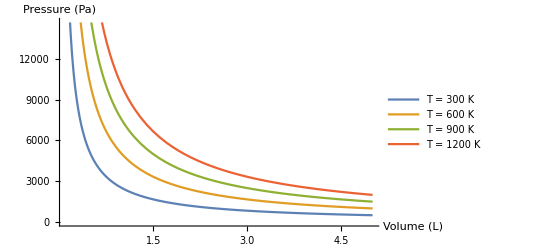

```mathematica
(* Ideal Gas Law and State Variables *)
R=8.314;
n=1;
P[V_,T_]:=n R T/V;

(* Plot P vs V for different T *)
Plot[Evaluate[Table[P[V,T],{T,{300,600,900,1200}}]],{V,0.1,5},PlotLegends->Placed[{"T = 300 K","T = 600 K","T = 900 K","T = 1200 K"},Above],AxesLabel->{"Volume (L)","Pressure (Pa)"}]
```

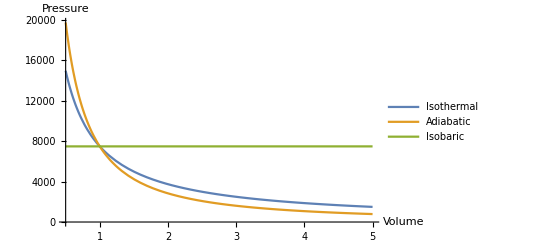

```mathematica
(* PV Diagrams for Common Thermodynamic Processes *)
T=900;gamma=1.4;V0=1;
P0=P[V0,T];
adiabatic[V_]:=P0 (V0/V)^1.4;
isothermal[V_]:=P0 (V0/V);
isobaric[V_]:=P0;

Plot[{isothermal[V],adiabatic[V],isobaric[V]},{V,0.5,5},PlotLegends->{"Isothermal","Adiabatic","Isobaric"},AxesLabel->{"Volume","Pressure"}]
```

```mathematica
(* Heat Equation *)
heqn=D[u[x,t],t]==D[u[x,t],{x,2}];

(* Initial condition *)
ic=u[x,0]==E^(-x^2);

(* Solve *) 
sol=DSolveValue[{heqn,ic},u[x,t],{x,t}]
Plot3D[sol,{x,-5,5},{t,0,2},AxesLabel->{"x","t","u"},PlotRange->All, Mesh->None]
```

(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))

-Graphics3D-